D:\Development\Math in Chemistry\1DQuantumSystems\Morse

12

100

0.185001 (1-ⅇ^(-1.21023 (-1.77993+x)))^2

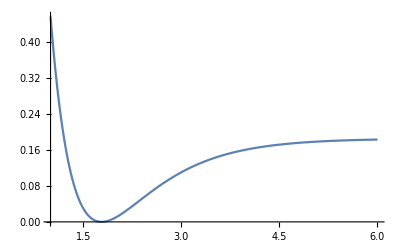

```mathematica
SetDirectory[NotebookDirectory[]]
L=12
Nt=100

potentialFun[x_]=0.001593601*116.09*(1-Exp[-2.287*0.5291772108*(x-0.9419/0.5291772108)])^2
Plot[potentialFun[x],{x,1,L/2}]
```

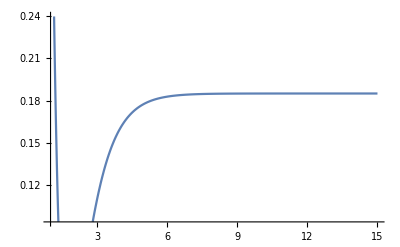

-Graphics-

```mathematica
sinBasis=Table[Sqrt[2/L]Sin[π i (x+L/2)/L],{i,Nt}]
kineticEnerOperator[f_,x_]:=(-D[f,{x,2}])/(2*1728.16)
harmonicOperator[f_,x_]:=kineticEnerOperator[f,x]+potentialFun[x]*f
hamiltonianMatrix=Table[NIntegrate[sinBasis[[m]] harmonicOperator[sinBasis[[n]],x],{x,-L/2,L/2}],{m,Nt},{n,Nt}]

{Energy,Coeff}=Eigensystem[hamiltonianMatrix,-20]
eigxp=Coeff.sinBasis
```

{Sin[1/12 π (6+x)]/(√6),Sin[1/6 π (6+x)]/(√6),Sin[1/4 π (6+x)]/(√6),Sin[1/3 π (6+x)]/(√6),Sin[5/12 π (6+x)]/(√6),Sin[1/2 π (6+x)]/(√6),Sin[7/12 π (6+x)]/(√6),Sin[2/3 π (6+x)]/(√6),Sin[3/4 π (6+x)]/(√6),Sin[5/6 π (6+x)]/(√6),Sin[11/12 π (6+x)]/(√6),Sin[π (6+x)]/(√6),Sin[13/12 π (6+x)]/(√6),Sin[7/6 π (6+x)]/(√6),Sin[5/4 π (6+x)]/(√6),Sin[4/3 π (6+x)]/(√6),Sin[17/12 π (6+x)]/(√6),Sin[3/2 π (6+x)]/(√6),Sin[19/12 π (6+x)]/(√6),Sin[5/3 π (6+x)]/(√6),Sin[7/4 π (6+x)]/(√6),Sin[11/6 π (6+x)]/(√6),Sin[23/12 π (6+x)]/(√6),Sin[2 π (6+x)]/(√6),Sin[25/12 π (6+x)]/(√6),Sin[13/6 π (6+x)]/(√6),Sin[9/4 π (6+x)]/(√6),Sin[7/3 π (6+x)]/(√6),Sin[29/12 π (6+x)]/(√6),Sin[5/2 π (6+x)]/(√6),Sin[31/12 π (6+x)]/(√6),Sin[8/3 π (6+x)]/(√6),Sin[11/4 π (6+x)]/(√6),Sin[17/6 π (6+x)]/(√6),Sin[35/12 π (6+x)]/(√6),Sin[3 π (6+x)]/(√6),Sin[37/12 π (6+x)]/(√6),Sin[19/6 π (6+x)]/(√6),Sin[13/4 π (6+x)]/(√6),Sin[10/3 π (6+x)]/(√6),Sin[41/12 π (6+x)]/(√6),Sin[7/2 π (6+x)]/(√6),Sin[43/12 π (6+x)]/(√6),Sin[11/3 π (6+x)]/(√6),Sin[15/4 π (6+x)]/(√6),Sin[23/6 π (6+x)]/(√6),Sin[47/12 π (6+x)]/(√6),Sin[4 π (6+x)]/(√6),Sin[49/12 π (6+x)]/(√6),Sin[25/6 π (6+x)]/(√6),Sin[17/4 π (6+x)]/(√6),Sin[13/3 π (6+x)]/(√6),Sin[53/12 π (6+x)]/(√6),Sin[9/2 π (6+x)]/(√6),Sin[55/12 π (6+x)]/(√6),Sin[14/3 π (6+x)]/(√6),Sin[19/4 π (6+x)]/(√6),Sin[29/6 π (6+x)]/(√6),Sin[59/12 π (6+x)]/(√6),Sin[5 π (6+x)]/(√6),Sin[61/12 π (6+x)]/(√6),Sin[31/6 π (6+x)]/(√6),Sin[21/4 π (6+x)]/(√6),Sin[16/3 π (6+x)]/(√6),Sin[65/12 π (6+x)]/(√6),Sin[11/2 π (6+x)]/(√6),Sin[67/12 π (6+x)]/(√6),Sin[17/3 π (6+x)]/(√6),Sin[23/4 π (6+x)]/(√6),Sin[35/6 π (6+x)]/(√6),Sin[71/12 π (6+x)]/(√6),Sin[6 π (6+x)]/(√6),Sin[73/12 π (6+x)]/(√6),Sin[37/6 π (6+x)]/(√6),Sin[25/4 π (6+x)]/(√6),Sin[19/3 π (6+x)]/(√6),Sin[77/12 π (6+x)]/(√6),Sin[13/2 π (6+x)]/(√6),Sin[79/12 π (6+x)]/(√6),Sin[20/3 π (6+x)]/(√6),Sin[27/4 π (6+x)]/(√6),Sin[41/6 π (6+x)]/(√6),Sin[83/12 π (6+x)]/(√6),Sin[7 π (6+x)]/(√6),Sin[85/12 π (6+x)]/(√6),Sin[43/6 π (6+x)]/(√6),Sin[29/4 π (6+x)]/(√6),Sin[22/3 π (6+x)]/(√6),Sin[89/12 π (6+x)]/(√6),Sin[15/2 π (6+x)]/(√6),Sin[91/12 π (6+x)]/(√6),Sin[23/3 π (6+x)]/(√6),Sin[31/4 π (6+x)]/(√6),Sin[47/6 π (6+x)]/(√6),Sin[95/12 π (6+x)]/(√6),Sin[8 π (6+x)]/(√6),Sin[97/12 π (6+x)]/(√6),Sin[49/6 π (6+x)]/(√6),Sin[33/4 π (6+x)]/(√6),Sin[25/3 π (6+x)]/(√6)}

{1}
 |  |  |  |

{{0.190271,0.183552,0.182707,0.177891,0.1724,0.167845,0.160961,0.147534,0.142721,0.134402,0.122448,0.113612,0.0942147,0.0881525,0.0711326,0.0570001,0.0443009,0.0299773,0.0172112,-0.0135826},{{0.0236474,-0.0160143,-0.010872,0.0179116,0.00789433,-0.0367005,0.0381093,-0.0231579,0.0272357,-0.0577705,0.0804612,-0.0648969,0.0271827,-0.00980048,0.0253864,-0.0421043,0.0317158,-0.0139511,0.0339002,-0.100932,0.172477,-0.206463,0.212266,-0.231082,0.272859,-0.296574,0.261548,-0.180261,0.101184,-0.0461161,-0.0114549,0.0975254,-0.18667,0.221503,-0.179299,0.0978788,-0.0275918,-0.0244838,0.0836955,-0.149439,0.175111,-0.120179,0.00778422,0.0902416,-0.12494,0.109091,-0.079918,0.0437972,0.0192923,-0.101584,0.147076,-0.105164,-0.00437641,0.100771,-0.120567,0.0729509,-0.0115886,-0.0313236,0.0626598,-0.0863315,0.0747175,-0.00446655,-0.0900456,0.128978,-0.0676582,-0.0467955,0.11641,-0.0894499,0.00488544,0.0598468,-0.068329,0.041446,-0.00952591,-0.0231842,0.0577602,-0.0686721,0.0238623,0.0596892,-0.107152,0.0581435,0.0548481,-0.123605,0.0742407,0.0482947,-0.121672,0.0740235,0.0415137,-0.106603,0.0630247,0.0338307,-0.0837504,0.0477151,0.0238903,-0.0578537,0.0337742,0.0106101,-0.0327074,0.02599,-0.010536,0.00186139},{-0.0197653,0.00546639,0.030059,-0.0446169,0.024205,-0.00113207,0.00817799,-0.033057,0.0369146,-0.0109533,-0.00899814,-0.00778624,0.0416842,-0.0468875,0.0135401,0.0182727,-0.0122337,-0.0191054,0.0415175,-0.0568083,0.10312,-0.192666,0.275828,-0.288819,0.22606,-0.141073,0.0753241,-0.0121183,-0.0826443,0.191426,-0.246565,0.205519,-0.101711,0.00432441,0.0581794,-0.109901,0.165093,-0.184927,0.120143,0.0141741,-0.13481,0.170079,-0.125802,0.0592211,-0.00347196,-0.0547805,0.122029,-0.154767,0.0993388,0.0302536,-0.143223,0.156012,-0.073751,-0.0257859,0.0794141,-0.0877661,0.0778815,-0.0480553,-0.0207992,0.10671,-0.136949,0.0620607,0.0715227,-0.150635,0.106959,0.0135679,-0.102503,0.0990946,-0.0343742,-0.0258471,0.0534891,-0.0601269,0.0493419,-0.00437092,-0.0671547,0.105891,-0.0536342,-0.0641101,0.138117,-0.0834327,-0.0581461,0.147676,-0.0924128,-0.0523009,0.139345,-0.085087,-0.0464709,0.118889,-0.0685692,-0.0389501,0.0917087,-0.0498021,-0.0282188,0.0626956,-0.0345241,-0.0133251,0.035681,-0.0274611,0.0108718,-0.00187873},{0.0468896,-0.0746705,0.0912401,-0.122153,0.177999,-0.24238,0.294472,-0.331844,0.360651,-0.369763,0.332209,-0.240634,0.132129,-0.0643074,0.0637482,-0.103614,0.13454,-0.133129,0.115615,-0.106747,0.105122,-0.086951,0.0404264,0.0156768,-0.0533805,0.0675156,-0.0755852,0.0872623,-0.0869636,0.0547395,0.00242848,-0.0521326,0.0703393,-0.0637102,0.0526746,-0.0407118,0.0130185,0.0340579,-0.0753225,0.0787544,-0.0414273,-0.00665627,0.0356489,-0.0433611,0.0444381,-0.0411135,0.0191019,0.0249631,-0.0646994,0.065229,-0.0222776,-0.0298187,0.0528582,-0.0408138,0.016058,0.00325123,-0.0193736,0.0370304,-0.0430979,0.018768,0.0288653,-0.0614255,0.0457997,0.00737711,-0.0510682,0.0494152,-0.0116794,-0.0238919,0.0325353,-0.020952,0.00671379,0.00597044,-0.0214676,0.032225,-0.019783,-0.0175641,0.0490111,-0.0379401,-0.0134125,0.0569642,-0.0462925,-0.0109764,0.0573762,-0.0457509,-0.010335,0.0521034,-0.0390517,-0.0103078,0.0429042,-0.0293123,-0.00953905,0.0314949,-0.0194187,-0.00691906,0.0193447,-0.0114847,-0.0018243,0.00690139,-0.0042271,0.000961287},{-0.0197549,0.0738982,-0.145552,0.185912,-0.177798,0.156321,-0.158625,0.172241,-0.153472,0.0906401,-0.0249655,-0.0000538887,-0.00849168,0.0096187,0.0108325,-0.0228469,0.0041319,0.0134996,0.0246549,-0.122285,0.214797,-0.237079,0.191607,-0.130984,0.0829927,-0.0214992,-0.0789906,0.183969,-0.221813,0.164065,-0.05868,-0.0267842,0.075978,-0.117252,0.156759,-0.151144,0.0638151,0.0698277,-0.16133,0.156378,-0.0837406,0.00904852,0.0405475,-0.083299,0.123377,-0.119769,0.0369527,0.0882277,-0.161647,0.124335,-0.0140649,-0.077994,0.100617,-0.0747416,0.0397624,0.000633244,-0.059331,0.111503,-0.0981051,-0.000409619,0.115066,-0.142628,0.0535829,0.0716012,-0.124257,0.0747952,0.013049,-0.0638604,0.062168,-0.03821,0.00985695,0.0304257,-0.0735563,0.0744416,-0.00328652,-0.0934135,0.118002,-0.0273297,-0.101431,0.137772,-0.0375942,-0.100943,0.136777,-0.0358628,-0.0939645,0.120794,-0.0269832,-0.0816212,0.0962879,-0.0164183,-0.0648344,0.0691622,-0.00863514,-0.0448507,0.0442519,-0.00660203,-0.0230376,0.0245684,-0.0115742,0.00228392},{-0.142952,0.276985,-0.378282,0.416444,-0.377688,0.274818,-0.134556,-0.0171962,0.153262,-0.238146,0.241207,-0.167002,0.0671087,-0.00933827,0.0268,-0.09395,0.151069,-0.153635,0.103552,-0.0379941,-0.00960123,0.0361919,-0.0576424,0.0774836,-0.0775525,0.0428826,0.0127354,-0.0558329,0.0666829,-0.054796,0.0388127,-0.0206113,-0.0106003,0.0515969,-0.0760117,0.0599334,-0.0113559,-0.0351074,0.0529426,-0.0453989,0.0303576,-0.0133606,-0.0132917,0.0466586,-0.0624773,0.0387312,0.0138893,-0.0558281,0.0565873,-0.0231959,-0.0127484,0.0301994,-0.0324731,0.0287137,-0.0153916,-0.0138371,0.0457423,-0.0503092,0.0136994,0.0381827,-0.0598799,0.0322766,0.0176232,-0.0457354,0.0347144,-0.00410187,-0.0182273,0.0239083,-0.0205977,0.0116514,0.00720573,-0.0305315,0.0362164,-0.00835047,-0.0352952,0.0519525,-0.0185992,-0.0366727,0.0584413,-0.0224297,-0.0358774,0.0571545,-0.0209945,-0.0333587,0.0503303,-0.0164683,-0.0292242,0.040394,-0.0111862,-0.023527,0.0295069,-0.00699478,-0.0165636,0.019489,-0.00515775,-0.0087507,0.0116778,-0.00693429,0.00217109,-0.000284961},{-0.0345499,0.0261115,0.0101665,-0.0221414,-0.00823752,0.0413555,-0.0354508,0.00367066,0.00664457,0.0168602,-0.032015,0.00207968,0.0476622,-0.0585789,0.0168569,0.0260946,-0.0197418,-0.0251074,0.0640494,-0.0891634,0.134049,-0.203831,0.236369,-0.16442,0.00563931,0.140966,-0.194868,0.166482,-0.116403,0.0663265,0.014058,-0.131063,0.21687,-0.188469,0.0486262,0.102858,-0.168106,0.140382,-0.0803436,0.0253822,0.0410623,-0.126578,0.175747,-0.117979,-0.0340964,0.169081,-0.180509,0.0732251,0.0518158,-0.109253,0.0998523,-0.0683598,0.0272409,0.0423537,-0.122972,0.140713,-0.0448529,-0.107084,0.182212,-0.106227,-0.0525709,0.151301,-0.117159,0.00652306,0.0752148,-0.0838483,0.0510365,-0.0138415,-0.0284535,0.0773659,-0.0920402,0.0262782,0.090075,-0.146911,0.0652785,0.0951162,-0.175326,0.0831289,0.0961204,-0.179851,0.081843,0.0940643,-0.165952,0.0676305,0.0882925,-0.13998,0.0477755,0.077997,-0.108165,0.0287317,0.0629907,-0.0758699,0.0150407,0.044091,-0.0474286,0.00935845,0.0225859,-0.0253525,0.0121739,-0.00242973},{-0.086929,0.112647,-0.0839745,0.0550797,-0.0492931,0.0312291,0.0336935,-0.116369,0.147708,-0.10121,0.0257039,0.014445,-0.0114699,0.00589098,-0.01816,0.0221083,0.00182047,-0.0154421,-0.0399104,0.156023,-0.24073,0.209079,-0.0769207,-0.058984,0.127315,-0.140409,0.140258,-0.120098,0.0368158,0.102964,-0.209891,0.193147,-0.0622588,-0.0791473,0.141533,-0.126556,0.0877514,-0.0443604,-0.0286347,0.127445,-0.179791,0.113522,0.0443015,-0.171557,0.1689,-0.0568317,-0.0591913,0.10481,-0.0919283,0.0631666,-0.0217795,-0.0516277,0.129442,-0.132578,0.0219074,0.12715,-0.179562,0.0806098,0.0795621,-0.157135,0.0995371,0.017325,-0.0873425,0.0801084,-0.0384008,-0.000179705,0.039215,-0.0793085,0.0797866,-0.00382538,-0.105497,0.138103,-0.0353225,-0.120115,0.169807,-0.049758,-0.12593,0.176528,-0.0483878,-0.124429,0.163621,-0.0364417,-0.116234,0.137877,-0.0202941,-0.101963,0.106061,-0.0055546,-0.0827221,0.0739788,0.00393192,-0.0602466,0.0461019,0.00618272,-0.0365998,0.0254044,0.00055849,-0.0121661,0.00802448,-0.00188222},{0.0118734,0.0131933,-0.0541223,0.0554451,-0.00209145,-0.0563358,0.0660962,-0.0341911,0.0114403,-0.0193796,0.0232211,0.0117359,-0.061287,0.0684865,-0.0229097,-0.0182183,0.000680798,0.0602741,-0.108576,0.125241,-0.139532,0.159338,-0.132679,0.0135532,0.149436,-0.232994,0.163631,-3.088×10^-6,-0.128995,0.154417,-0.110602,0.0568292,0.00160961,-0.0867087,0.167584,-0.159856,0.0272605,0.144235,-0.212241,0.121935,0.0390618,-0.138058,0.127716,-0.0615946,0.00106612,0.0497472,-0.103788,0.125835,-0.0578507,-0.0852093,0.187418,-0.13882,-0.0342389,0.177703,-0.163256,0.0175409,0.116311,-0.132249,0.0522512,0.031263,-0.0662164,0.0673452,-0.0535312,0.00917711,0.0696194,-0.123165,0.0733313,0.0676179,-0.170891,0.114706,0.0671248,-0.195724,0.130673,0.0697469,-0.19995,0.124887,0.073995,-0.187633,0.104349,0.0770197,-0.163582,0.0767685,0.0762757,-0.132781,0.0488845,0.0703854,-0.0998528,0.0255443,0.059375,-0.0687114,0.00955737,0.0443653,-0.0423327,0.00199659,0.0270585,-0.0226827,0.00288777,0.00780569,-0.00585202,0.00143933},{0.196069,-0.271145,0.209033,-0.0861524,-0.0269228,0.119694,-0.197227,0.223809,-0.152499,0.00587176,0.114179,-0.123237,0.0462311,0.0122381,0.0146233,-0.0925706,0.145384,-0.14955,0.143468,-0.151617,0.136372,-0.0486045,-0.0884391,0.178608,-0.148742,0.0283938,0.0829356,-0.118676,0.0940273,-0.054779,0.0101908,0.0568076,-0.126937,0.133845,-0.0390258,-0.10017,0.169066,-0.109967,-0.0189284,0.108478,-0.107892,0.0532583,0.000196654,-0.0404022,0.0788259,-0.0961321,0.0490233,0.0589159,-0.14431,0.116368,0.0165951,-0.138258,0.137889,-0.0234368,-0.092665,0.113999,-0.0477455,-0.0284327,0.0603971,-0.0551045,0.0364823,-0.00252012,-0.0518716,0.0908648,-0.0578922,-0.0457614,0.129474,-0.0956741,-0.042175,0.151312,-0.112881,-0.0428292,0.157695,-0.111672,-0.0466129,0.151263,-0.0972045,-0.0509538,0.135248,-0.0755078,-0.0533307,0.113186,-0.0521429,-0.0520622,0.0884914,-0.0313011,-0.0466933,0.0642418,-0.0156297,-0.0377592,0.0428627,-0.00627339,-0.0265188,0.0261538,-0.00337969,-0.0143783,0.0152727,-0.00747277,0.00171601,-0.0000973068},{0.185193,-0.296662,0.279324,-0.128224,-0.0894622,0.259285,-0.290296,0.178105,-0.00433935,-0.126757,0.158289,-0.103728,0.0204835,0.0300976,-0.0104756,-0.0750401,0.171963,-0.199855,0.116034,0.0330361,-0.1402,0.133695,-0.040923,-0.0510544,0.0874549,-0.0808685,0.061615,-0.0260825,-0.0422748,0.115937,-0.125329,0.036325,0.0914766,-0.15046,0.0928484,0.0226249,-0.0975724,0.0919593,-0.0422176,-0.00380456,0.0386357,-0.0719324,0.0832164,-0.0346803,-0.0636167,0.131807,-0.093265,-0.0323724,0.133383,-0.116432,0.00292569,0.0973502,-0.102142,0.0300509,0.0405198,-0.0614686,0.0455262,-0.0207546,-0.0106447,0.052162,-0.0747885,0.0358814,0.0547121,-0.115036,0.0688108,0.0569293,-0.139226,0.084748,0.0602227,-0.147913,0.0849438,0.0640248,-0.14344,0.0735218,0.0667173,-0.12907,0.0556187,0.0667191,-0.10845,0.0360685,0.0631206,-0.0850982,0.0185588,0.0559397,-0.0620671,0.00535725,0.0459673,-0.0416855,-0.00261229,0.034459,-0.0254853,-0.00544987,0.0228087,-0.014298,-0.00384166,0.0122412,-0.00846788,0.00211671,0.00041658,-0.000270703},{-0.0842012,0.0889514,-0.0237682,-0.0336803,0.0356534,-0.0111542,0.00832789,-0.0210554,0.0043046,0.046575,-0.0719416,0.023777,0.0589162,-0.0864532,0.0292684,0.0415707,-0.0405229,-0.0321354,0.103973,-0.127094,0.119352,-0.10439,0.0569302,0.0517811,-0.171213,0.187991,-0.0517375,-0.140449,0.222675,-0.127359,-0.0491521,0.155005,-0.133343,0.0465605,0.0263346,-0.0709069,0.104154,-0.103825,0.0245331,0.111693,-0.189626,0.110103,0.0807908,-0.211453,0.155486,0.0327857,-0.174637,0.152094,-0.0145305,-0.0986496,0.109488,-0.0519816,-0.00678006,0.0469295,-0.078493,0.081296,-0.0158225,-0.0970076,0.15229,-0.0641874,-0.110949,0.199597,-0.0911264,-0.122023,0.221929,-0.0964017,-0.130046,0.221826,-0.0845429,-0.133686,0.204095,-0.0622733,-0.131632,0.174627,-0.0364362,-0.123365,0.139328,-0.0125291,-0.109509,0.103392,0.00592357,-0.0916458,0.0707804,0.0174224,-0.071899,0.0440424,0.0220962,-0.0524446,0.0243786,0.021131,-0.035135,0.0119087,0.0162227,-0.0213554,0.00610063,0.00906303,-0.0120172,0.00680172,-0.00194073,0.000210735},{0.0349064,-0.0903536,0.12147,-0.0613321,-0.0751905,0.173632,-0.133345,-0.0162586,0.140799,-0.142093,0.0502914,0.0317248,-0.0483652,0.0286367,-0.0177789,0.0158215,-0.0045834,0.0042998,-0.0562782,0.143813,-0.172893,0.0699636,0.11045,-0.214636,0.144156,0.0365368,-0.166331,0.151253,-0.0400461,-0.057679,0.0915582,-0.0860372,0.0635952,-0.00582431,-0.0900728,0.154867,-0.100396,-0.0618081,0.193818,-0.160331,-0.0195808,0.178799,-0.171627,0.0200154,0.122807,-0.138626,0.048467,0.0444564,-0.0772558,0.0651373,-0.0383626,-0.0072304,0.0742254,-0.112159,0.0545782,0.0807063,-0.168553,0.0974348,0.0878374,-0.203865,0.117513,0.0962007,-0.217995,0.116584,0.10434,-0.213455,0.100002,0.109893,-0.194366,0.074502,0.110823,-0.165669,0.0465131,0.106123,-0.132324,0.0210121,0.0960648,-0.0987235,0.00109118,0.0819403,-0.0682273,-0.0120282,0.0656361,-0.0429939,-0.0185814,0.0491083,-0.0239845,-0.019758,0.0340329,-0.0112108,-0.0171502,0.0215801,-0.00402215,-0.0123888,0.0124482,-0.00149286,-0.00683795,0.00697127,-0.0031815,0.000609543},{0.1128,-0.130153,0.0475517,0.0547742,-0.0988134,0.0736202,-0.0171228,-0.0393935,0.0864971,-0.10828,0.0755577,0.0117726,-0.095003,0.104761,-0.0456835,0.00449131,-0.0521468,0.154954,-0.210728,0.16625,-0.0667321,-0.0150889,0.0609909,-0.0914186,0.0954241,-0.0302027,-0.0948173,0.176306,-0.109498,-0.0756167,0.211493,-0.157626,-0.0425527,0.197568,-0.165333,-0.0059901,0.144038,-0.137253,0.0284548,0.0655585,-0.0856566,0.0583114,-0.0211761,-0.026548,0.0841826,-0.102078,0.0261514,0.106952,-0.166725,0.0628757,0.127079,-0.209521,0.0799322,0.14367,-0.228927,0.0784428,0.155199,-0.226973,0.0630556,0.159974,-0.207932,0.0398223,0.157091,-0.177398,0.0147446,0.146666,-0.141089,-0.00751326,0.130009,-0.104148,-0.024036,0.10919,-0.0704692,-0.0337739,0.0866686,-0.0425495,-0.0371097,0.0647251,-0.0214446,-0.0354014,0.04517,-0.00707976,-0.0303845,0.0291094,0.0014366,-0.0237804,0.0169866,0.00538824,-0.0169808,0.00867925,0.00615657,-0.0109662,0.00372683,0.00497279,-0.00631135,0.00152174,0.00281122,-0.00328403,0.00158455,-0.000314974},{0.0112653,-0.068767,0.116697,-0.0565306,-0.100867,0.204886,-0.125362,-0.0830473,0.224299,-0.173172,0.00589449,0.101495,-0.0744919,0.000574732,0.00135714,0.0779621,-0.151334,0.15494,-0.108184,0.0561874,-0.00179334,-0.0705597,0.126635,-0.092621,-0.0435982,0.173836,-0.159559,-0.010189,0.182068,-0.187357,0.0206794,0.153236,-0.173594,0.0429853,0.0970959,-0.127201,0.0565665,0.0254433,-0.0623032,0.0641399,-0.0494585,0.00533665,0.0700242,-0.117644,0.062879,0.077374,-0.171751,0.102023,0.087521,-0.207709,0.119925,0.0995181,-0.224242,0.118146,0.111107,-0.222681,0.10141,0.119537,-0.206161,0.0757572,0.122674,-0.179037,0.0472097,0.119456,-0.146011,0.0206145,0.110149,-0.111529,-0.000802712,0.0960409,-0.079178,-0.0155865,0.0790771,-0.0514446,-0.0237255,0.0613148,-0.0296009,-0.0262492,0.044565,-0.013884,-0.0246899,0.0301035,-0.00372967,-0.0206873,0.0186246,0.00187623,-0.01566,0.0102772,0.00412395,-0.0106769,0.0048373,0.00413169,-0.00641924,0.00187255,0.00282605,-0.00325846,0.000929741,0.000707334,-0.000683646,0.000181533},{-0.153743,0.184112,-0.0709032,-0.0917291,0.179666,-0.137036,0.00610304,0.120594,-0.170733,0.130134,-0.0370207,-0.0477028,0.0779675,-0.0575845,0.0464664,-0.109318,0.233809,-0.310667,0.231293,-0.0188389,-0.164255,0.168036,-0.00982038,-0.143717,0.149838,-0.0256609,-0.0940366,0.109555,-0.0408995,-0.0294354,0.0571224,-0.0554921,0.0390692,0.00472636,-0.0716079,0.103119,-0.0389384,-0.0890983,0.155088,-0.0675929,-0.107406,0.190692,-0.0794928,-0.124354,0.207919,-0.0758634,-0.137734,0.207715,-0.0606757,-0.145287,0.192784,-0.0387893,-0.145807,0.167328,-0.0152223,-0.139032,0.135876,0.00607183,-0.125946,0.102843,0.0224124,-0.108253,0.0717533,0.032699,-0.0881641,0.0451121,0.0370295,-0.0678045,0.0241825,0.0364562,-0.0489959,0.00923674,0.0324345,-0.0329441,-0.000287419,0.0265312,-0.0202751,-0.00539091,0.0200657,-0.0110294,-0.00729038,0.0140277,-0.00487287,-0.00712623,0.00898571,-0.00121709,-0.00586835,0.00518732,0.000575464,-0.00421051,0.00261465,0.00111395,-0.00261747,0.00113135,0.000876243,-0.00133997,0.000548462,0.000147653,-0.000223129,0.0000647043},{-0.122078,0.0819608,0.0703753,-0.135134,0.0206912,0.134434,-0.134195,-0.0267419,0.155375,-0.101952,-0.0574069,0.124896,-0.0311037,-0.0887368,0.0776326,0.0463641,-0.12442,0.0593109,0.0769107,-0.145264,0.0992366,-0.00777039,-0.0512978,0.0678279,-0.0636851,0.0314241,0.0448018,-0.120971,0.104318,0.0321975,-0.174043,0.15941,0.0315141,-0.217578,0.192005,0.0416569,-0.247694,0.201525,0.0591498,-0.262098,0.190623,0.0795014,-0.26057,0.164367,0.0981652,-0.244702,0.128878,0.111582,-0.217615,0.0902677,0.117634,-0.18327,0.053659,0.115844,-0.14586,0.0226941,0.107099,-0.109154,-0.000681541,0.0932447,-0.076092,-0.0160428,0.0765295,-0.0485377,-0.0241539,0.0591533,-0.0272899,-0.0264969,0.0429006,-0.0122277,-0.0248477,0.0289759,-0.00258824,-0.0209074,0.0179642,0.00275403,-0.0160825,0.00993092,0.00501501,-0.0113691,0.00456404,0.00531477,-0.00735984,0.00135013,0.00455518,-0.0043041,-0.00028726,0.00338681,-0.00221542,-0.000876979,0.00221974,-0.000968571,-0.000850265,0.00128209,-0.000392533,-0.000517634,0.000678788,-0.000360871,0.0000892128,-6.17293×10^-6},{-0.230843,0.223563,0.00476317,-0.210281,0.193158,-0.000921173,-0.151194,0.127909,-0.000637951,-0.0678068,0.0167914,0.0669344,-0.0750828,-0.000767809,0.0878548,-0.132908,0.141202,-0.124711,0.064615,0.0418207,-0.125241,0.0913993,0.0561752,-0.177421,0.127118,0.0704964,-0.217252,0.144358,0.0898594,-0.242441,0.143304,0.111043,-0.251827,0.127346,0.12986,-0.245598,0.100873,0.143257,-0.226125,0.0692098,0.149056,-0.196773,0.0371423,0.146687,-0.16171,0.00864317,0.136741,-0.124931,-0.0137912,0.12092,-0.0899626,-0.0289983,0.101402,-0.0593278,-0.037135,0.0805392,-0.0345451,-0.0392139,0.0603601,-0.0160707,-0.0368042,0.0424179,-0.00357578,-0.0315767,0.0276134,0.00385461,-0.0250786,0.0162812,0.00738671,-0.0185005,0.00825659,0.00824415,-0.0126506,0.00307594,0.00749666,-0.00793633,0.000105208,0.00599617,-0.00447029,-0.00129574,0.00432131,-0.00214315,-0.00170408,0.00282262,-0.000743267,-0.00156426,0.00165367,-0.0000166864,-0.00119459,0.000848999,0.000263652,-0.000786856,0.000365611,0.000285114,-0.000449249,0.000140162,0.000175859,-0.000225547,0.000111979,-0.0000225851},{0.288889,-0.253235,-0.0599173,0.292173,-0.189298,-0.115996,0.273576,-0.122096,-0.145368,0.22783,-0.0616402,-0.136268,0.146177,0.00493656,-0.10364,0.0201974,0.139833,-0.168392,0.00544954,0.183013,-0.187315,-0.00801956,0.198429,-0.179119,-0.0301462,0.204811,-0.159534,-0.0522418,0.200912,-0.132133,-0.0710801,0.187661,-0.100803,-0.0843977,0.166928,-0.0691484,-0.0911382,0.141298,-0.0402214,-0.0912632,0.113492,-0.0161074,-0.0856692,0.0860702,0.00207963,-0.0758055,0.0610616,0.0141891,-0.0634002,0.0398514,0.0207867,-0.0501119,0.0231039,0.0229318,-0.0373396,0.0108723,0.0218813,-0.0260675,0.00272296,0.0188852,-0.0168549,-0.0020628,0.0150063,-0.0098626,-0.0043304,0.0110492,-0.00495897,-0.00489618,0.00752656,-0.0018185,-0.00446342,0.00469988,-0.0000364709,-0.00356512,0.00262881,0.000796543,-0.00256486,0.00124677,0.0010328,-0.00167071,0.000417079,0.000946908,-0.000976664,-0.0000126765,0.000726306,-0.00049672,-0.000183672,0.000486547,-0.000204089,-0.000205777,0.00028546,-0.0000537771,-0.000157715,0.000146356,-2.90874×10^-6,-0.000087974,0.0000720774,-0.0000213559,-2.17741×10^-6,2.14032×10^-6},{0.112533,-0.147366,0.0642591,0.0928759,-0.194086,0.120493,0.0998502,-0.272184,0.20086,0.100907,-0.388001,0.402047,-0.119412,-0.231236,0.397216,-0.329037,0.178514,-0.104769,0.119549,-0.122084,0.0468897,0.0570311,-0.0916791,0.0282709,0.0595075,-0.0779347,0.0133854,0.0594883,-0.063775,0.00150285,0.0558024,-0.0490145,-0.0078169,0.0499683,-0.035411,-0.0138444,0.042384,-0.0233621,-0.017141,0.0342652,-0.0136392,-0.0179131,0.0261778,-0.00620883,-0.0169455,0.0188913,-0.00111329,-0.0147473,0.0126745,0.00205632,-0.0120087,0.00779613,0.00362302,-0.00912883,0.0041797,0.00409249,-0.00650637,0.00174729,0.00382039,-0.00428907,0.000241858,0.00318832,-0.0025936,-0.000537057,0.00241232,-0.00137462,-0.000846563,0.00168433,-0.000590767,-0.000852213,0.00106812,-0.000125427,-0.000719891,0.00061453,0.0000991948,-0.000529626,0.000300372,0.000183798,-0.000354249,0.000114008,0.000180409,-0.000208116,0.0000106443,0.00014604,-0.000109393,-0.0000298832,0.0000983647,-0.0000444075,-0.0000411832,0.0000603016,-0.0000125733,-0.0000326773,0.0000298664,2.54082×10^-6,-0.0000219903,0.0000142663,2.29155×10^-6,-8.80843×10^-6,5.37737×10^-6,-1.21281×10^-6},{0.0494373,-0.0703575,0.0361248,0.0450626,-0.107895,0.080241,0.0251263,-0.0976388,0.0489059,0.0588542,-0.058904,-0.108193,0.268441,-0.179524,-0.160245,0.442552,-0.360685,-0.0330298,0.358304,-0.312416,-0.0131689,0.257843,-0.192348,-0.0628389,0.212379,-0.117997,-0.0830996,0.165035,-0.0626335,-0.0870945,0.121046,-0.0240446,-0.0806143,0.0832714,0.000508321,-0.0683362,0.0529968,0.0141268,-0.0538376,0.0303174,0.0198707,-0.0396074,0.0145233,0.020453,-0.027146,0.00443767,0.0180848,-0.0171628,-0.00127916,0.0144043,-0.00977962,-0.00392526,0.0105137,-0.00474956,-0.00461256,0.00705204,-0.0016292,-0.0042105,0.00431131,0.000077608,-0.00333101,0.00234214,0.000834502,-0.00236232,0.00105791,0.0010187,-0.00151227,0.000307526,0.00090858,-0.000864852,-0.0000683985,0.000685836,-0.000424982,-0.000210202,0.00045605,-0.000159192,-0.000223593,0.000267921,-0.0000195317,-0.00018068,0.000135852,0.0000387974,-0.00012342,0.0000544877,0.0000518826,-0.0000731731,0.0000116576,0.0000438832,-0.0000370581,-6.21252×10^-6,0.00002975,-0.0000154794,-9.71097×10^-6,0.0000168074,-5.39649×10^-6,-6.5991×10^-6,8.51282×10^-6,-4.23044×10^-6,8.62952×10^-7,-5.91829×10^-9}}}

{0.00965402 Sin[1/12 π (6+x)]-0.00653781 Sin[1/6 π (6+x)]-0.00443848 Sin[1/4 π (6+x)]+0.00731239 Sin[1/3 π (6+x)]+0.00322285 Sin[5/12 π (6+x)]-0.0149829 Sin[1/2 π (6+x)]+0.0155581 Sin[7/12 π (6+x)]-0.00945415 Sin[2/3 π (6+x)]+0.0111189 Sin[3/4 π (6+x)]-0.0235847 Sin[5/6 π (6+x)]+0.0328481 Sin[11/12 π (6+x)]-0.026494 Sin[π (6+x)]+115+0.0138113 Sin[15/2 π (6+x)]-0.0341909 Sin[91/12 π (6+x)]+0.0194796 Sin[23/3 π (6+x)]+0.00975317 Sin[31/4 π (6+x)]-0.0236187 Sin[47/6 π (6+x)]+0.0137883 Sin[95/12 π (6+x)]+0.00433156 Sin[8 π (6+x)]-0.0133527 Sin[97/12 π (6+x)]+0.0106104 Sin[49/6 π (6+x)]-0.00430131 Sin[33/4 π (6+x)]+0.000759908 Sin[25/3 π (6+x)],1,16,1,1}
 |  |  |  |

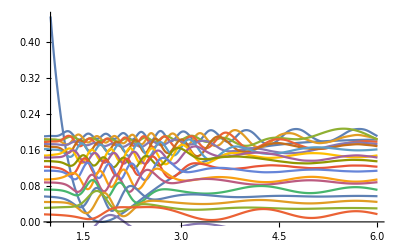

```mathematica
eigenPlot=Show[Plot[potentialFun[x],{x,1,L/2},PlotRange->Full],Plot[ Evaluate[0.02*eigxp+Energy],{x,0,L/2}]]
```

```mathematica
potentialEnergy=Table[NIntegrate[eigxp[[m]]* potentialFun[x]*eigxp[[m]],{x,-L/2,L/2}],{m,1,20}]
```

{0.15092,0.136517,0.170624,0.137265,0.160462,0.112319,0.107526,0.0913678,0.108931,0.102039,0.068776,0.0647489,0.0604328,0.057249,0.0635458,0.0318717,0.0295533,0.0129688,0.0908326,0.0432064}

{0.0393507,0.0470348,0.012083,0.0406262,0.0119382,0.055526,0.0534353,0.0561661,0.0337895,0.0323633,0.0536716,0.0488634,0.0337818,0.0309035,0.00758684,0.0251283,0.0147476,0.0170084,-0.0736215,-0.056789}

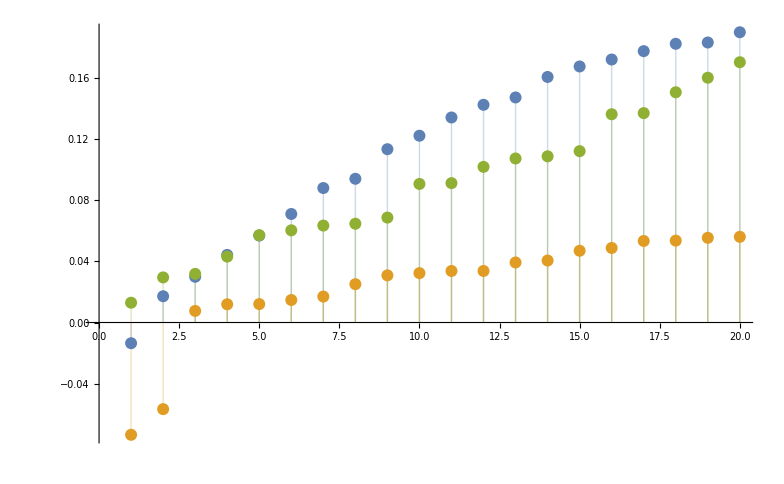

```mathematica
kineticEnergy=Table[Energy[[m]]-potentialEnergy[[m]],{m,1,20}]
Evaluate[ListPlot[{Sort[Energy],Sort[kineticEnergy],Sort[potentialEnergy]},Filling->Axis]]
```

```mathematica
β=1052.5822
averX=Table[NIntegrate[eigxp[[m]] x eigxp[[m]],{x,-L/2,L/2}],{m,1,20}]

ΔX=Table[Sqrt[NIntegrate[eigxp[[m]] x^2eigxp[[m]],{x,-L/2,L/2}]-averX[[m]]^2],{m,1,20}]
averP=Table[NIntegrate[eigxp[[m]] (-ⅈ *1728.16) *D[eigxp[[m]],x],{x,-L/2,L/2}],{m,1,20}]
ΔP=Table[Sqrt[NIntegrate[eigxp[[m]] *2*kineticEnerOperator[eigxp[[m]],x],{x,-L/2,L/2}]-averP[[m]]^2],{m,1,20}]
```

1052.58

{4.17581,3.63355,5.03079,3.70179,4.2742,3.03063,2.94269,2.69445,3.04758,2.9378,2.37627,2.34311,2.39866,2.28437,2.58286,1.88304,2.03817,1.77632,3.00805,2.11461}

{1.22178,1.10509,0.937878,1.16179,0.730304,0.955537,0.915023,0.88284,0.982478,0.772794,0.707494,0.652873,0.894659,0.788038,1.04271,0.404731,0.616034,0.326113,1.08008,0.647105}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.367}. NIntegrate obtained 0.-2.30045×10^-10 ⅈ and 2.58043×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.367}. NIntegrate obtained 0.-5.06539×10^-13 ⅈ and 3.60024×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.08575}. NIntegrate obtained 0.-1.93268×10^-12 ⅈ and 5.60759×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.-2.30045×10^-10 ⅈ,0.-5.06539×10^-13 ⅈ,0.-1.93268×10^-12 ⅈ,0.-5.46052×10^-12 ⅈ,0.-1.87635×10^-12 ⅈ,0.+5.10686×10^-12 ⅈ,0.-4.27747×10^-12 ⅈ,0.+3.29692×10^-12 ⅈ,0.+2.61658×10^-12 ⅈ,0.+1.55297×10^-12 ⅈ,0.+1.80653×10^-12 ⅈ,0.-7.95914×10^-11 ⅈ,0.-3.37623×10^-11 ⅈ,0.-1.84509×10^-12 ⅈ,0.+1.13884×10^-12 ⅈ,0.+2.82654×10^-11 ⅈ,0.+1.65845×10^-12 ⅈ,0.+2.38742×10^-12 ⅈ,0.+3.19744×10^-14 ⅈ,0.-1.13203×10^-12 ⅈ}

{0.280283+0. ⅈ,0.30875+0. ⅈ,0.136788+0. ⅈ,0.285962+0. ⅈ,0.121868+0. ⅈ,0.33721+0. ⅈ,0.326822+0. ⅈ,0.343736+0. ⅈ,0.272175+0. ⅈ,0.23905+0. ⅈ,0.336342+0. ⅈ,0.311456+0. ⅈ,0.295175+0. ⅈ,0.272269+0. ⅈ,0.22767+0. ⅈ,0.246169+0. ⅈ,0.197475+0. ⅈ,0.136804+0. ⅈ,0.0878026+0. ⅈ,0.123553+0. ⅈ}

1.61821×10^6

1.30307×10^-6

204.399 k

6.17968×10^-7 (1.87384×10^-77 (-0.0141049 Sin[1/12 π (6+x)]+0.01066 Sin[1/6 π (6+x)]+0.00415046 Sin[1/4 π (6+x)]-0.00903918 Sin[1/3 π (6+x)]-0.00336295 Sin[5/12 π (6+x)]+128+0.00382057 Sin[8 π (6+x)]+0.00922064 Sin[97/12 π (6+x)]-0.0103501 Sin[49/6 π (6+x)]+0.00496999 Sin[33/4 π (6+x)]-0.000991932 Sin[25/3 π (6+x)])^2+2.62915×10^-74 (-0.0354886 Sin[1/12 π (6+x)]+150)^2+1.23822×10^-84 (-0.00806915 Sin[1]+153)^2+8.54255×10^-44 (1)^2+12+3.01448×10^-84 1+3.61198×10^-68 (1)^2+1.05033×10^-87 (147+0.000759908 Sin[25/3 π (6+x)])^2+4.79045×10^-82 (-0.00806492 Sin[1/12 π (6+x)]+149+0.000932404 Sin[25/3 π (6+x)])^2)
 |  |  |  |

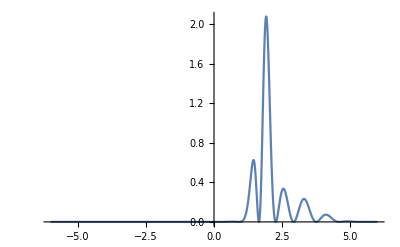

```mathematica
partitionFunc=Sum[Exp[-β Energy[[m]]],{m,1,20}]
EnsembleEnergy=Sum[Exp[-β Energy[[m]] Energy[[m]]]/partitionFunc,{m,1,20}]
heatCap=Sum[Quantity["BoltzmannConstant"] β^2  Energy[[m]]^2 Exp[-β Energy[[m]]],{m,1,20}]/partitionFunc
canonicalDistri=Sum[Exp[-β Energy[[m]] ]*eigxp[[m]]* eigxp[[m]],{m,1,20}]/partitionFunc
Evaluate[Plot[canonicalDistri,{x,-L/2,L/2},PlotRange->Full]]
```

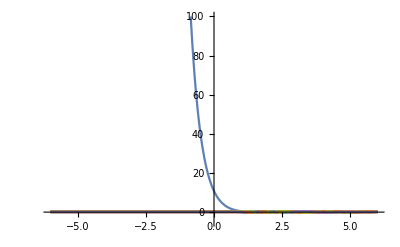

EigenFunction.jpg

Energy.txt

EnergyPlot.jpg

X_Fluctuation.txt

P_Fluctuation.txt

3.98025×10^-6

1.93311×10^-6

EnsembleEnergy.txt

HeatCapacity.txt

CanonicalLocationDistribution.jpg

```mathematica
Show[Plot[potentialFun[x],{x,-L/2,L/2},PlotRange->{-5,100}],Plot[ Evaluate[eigxp+Energy],{x,-L/2,L/2}]]
Export["EigenFunction.jpg",eigenPlot]
Export["Energy.txt",Table[Reverse[Energy],Reverse[kineticEnergy],Reverse[potentialEnergy]]]
Export["EnergyPlot.jpg",Evaluate[ListPlot[{Reverse[Energy],Reverse[kineticEnergy],Reverse[potentialEnergy]},Filling->Axis]]]
Export["X_Fluctuation.txt",Reverse[ΔX]]
Export["P_Fluctuation.txt",Reverse[ΔP]]
EnsembleKinetic=Sum[Exp[-β kineticEnergy[[m]] Energy[[m]]]/partitionFunc,{m,1,20}]
EnsemblePotential=Sum[Exp[-β Energy[[m]] potentialEnergy[[m]]]/partitionFunc,{m,1,20}]
Export["EnsembleEnergy.txt",Table[EnsembleEnergy,EnsembleKinetic,EnsemblePotential]]
Export["HeatCapacity.txt",heatCap]
Export["CanonicalLocationDistribution.jpg",Evaluate[Plot[canonicalDistri,{x,-L/2,L/2},PlotRange->Full]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["CanonicalLocationDistribution.jpg"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["CanonicalLocationDistribution.jpg"]]]
```

```mathematica
ScientificForm[partitionFunc]
```

9.09526

Part::pkspec1: The expression  cannot be used as a part specification.

$Aborted[]